```mathematica
SetDirectory[NotebookDirectory[]];
fileNames=FileNames["*_M.csv"];
rawData=Import[#]&/@fileNames;
labels=rawData[[1,1]]
```

{HH,Hh,HR,hh,hR,RR,TotSex,TotPop,}

```mathematica
transposed=Transpose[rawData[[All,2;;All]]];
Median/@transposed;
ListLinePlot[%//Transpose,PlotRange->All];
```

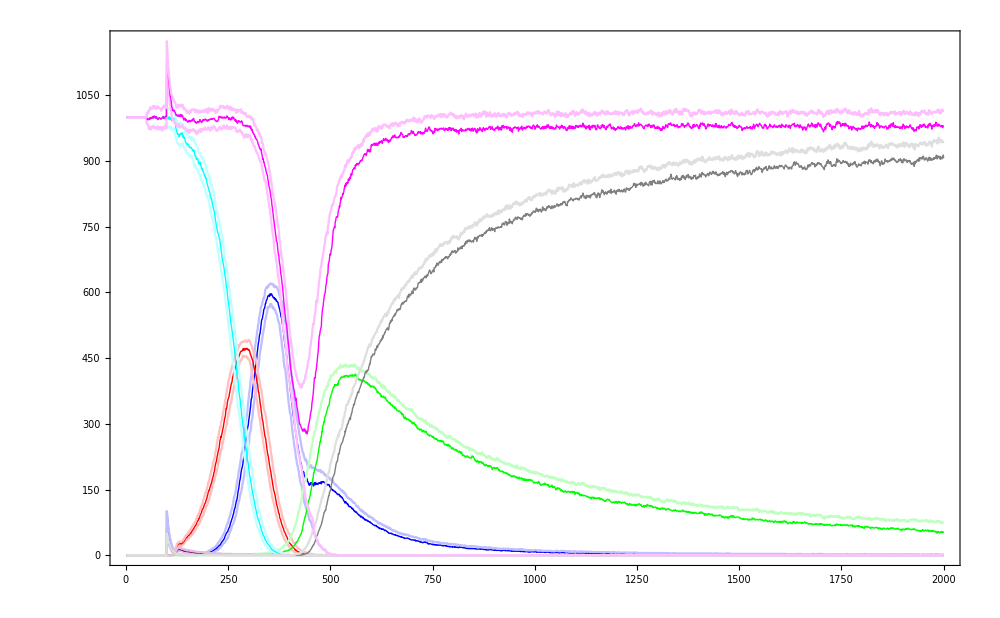
-Graphics- | HH | RGBColor[0, 0, 1]
Hh | RGBColor[1, 0, 0]
HR | RGBColor[0, 1, 0]
hh | RGBColor[0, 1, 1]
hR | RGBColor[0.5, 0, 0.5]
RR | GrayLevel[0.5]
TotSex | RGBColor[1, 0, 1]
TotPop | GrayLevel[0]

```mathematica
quartiles=Quartiles/@transposed;
colors={Blue,Red,Green,Cyan,Purple,Gray,Magenta,Black};
plot=Table[
ListLinePlot[
quartiles[[All,i]]//Transpose,
PlotStyle->{Lighter[colors[[i]],.75],{Thick,colors[[i]]},Lighter[colors[[i]],.75]},
PlotRange->All,
Frame->True,
FrameStyle->Thick
]
,{i,1,(quartiles[[1]]//Length)-1}]//Show[#,PlotRange->All,ImageSize->1000]&;
Grid[{{plot,Transpose[{labels[[1;;8]],colors}]//Grid}}]
```

{time,HH,Hh,HR,hh,hR,RR}

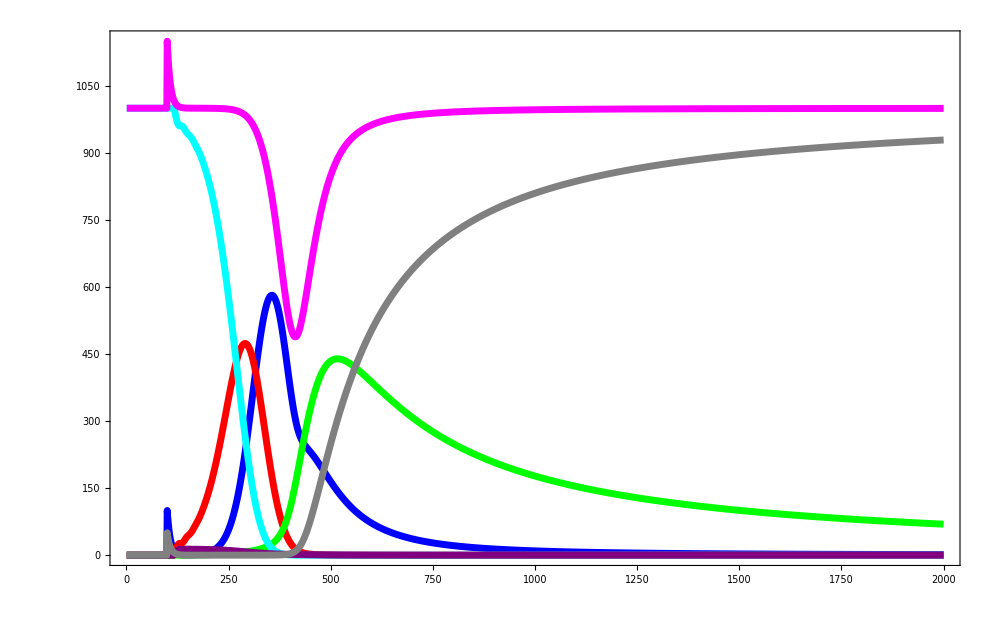

```mathematica
rawData2=Import["./OUT/ADM_Patch0000000001_Run1.csv"];
labels2=rawData2[[1]]
data2=rawData2[[2;;All,2;;All]];
data2Reshaped=Append[#[[1]],#[[2]]]&/@Transpose[{data2,Total/@data2}];
data2Reshaped=Prepend[data2Reshaped,data2Reshaped[[1]]];
plot=
ListLinePlot[
data2Reshaped//Transpose,
PlotStyle->(Directive[#,Thickness[.005]]&/@colors),
PlotRange->All,
Frame->True,
FrameStyle->Thick,
ImageSize->1000
]
```

```mathematica
quartile=2;
dataMatlab=quartiles[[All,1;;7,quartile]]//N;
plot2=ListLinePlot[
dataMatlab//Transpose,
PlotStyle->(Directive[#,Thickness[.005],Opacity[.25]]&/@colors),
PlotRange->All,
Frame->True,
FrameStyle->Thick,
ImageSize->1000
];
```

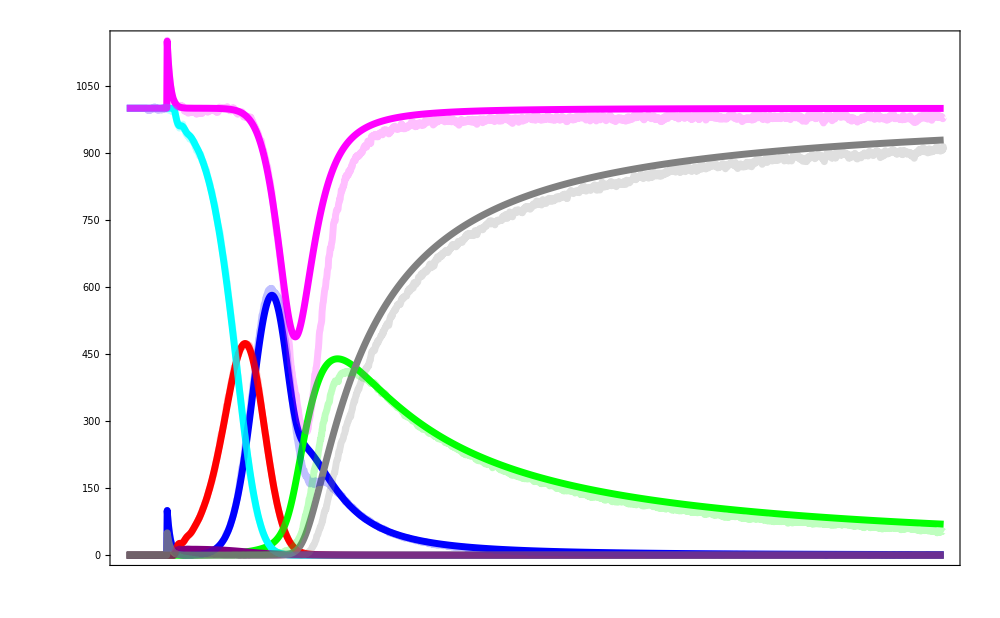
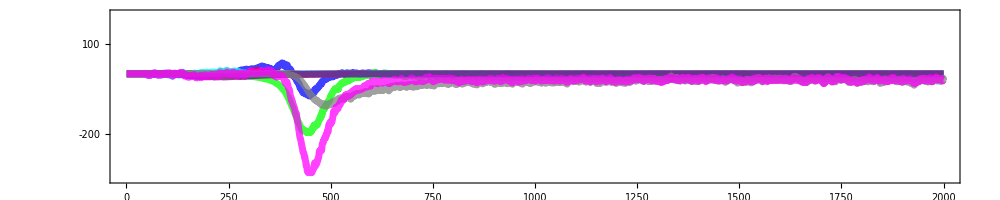
| Models Comparison | 
Time Responses | -Graphics- | Full Opacity: | MGDrivE (deterministic)
Half Opacity: | MatLab (stochastic)
Difference | -Graphics- | HH | RGBColor[0, 0, 1]
Hh | RGBColor[1, 0, 0]
HR | RGBColor[0, 1, 0]
hh | RGBColor[0, 1, 1]
hR | RGBColor[0.5, 0, 0.5]
RR | GrayLevel[0.5]
TotSex | RGBColor[1, 0, 1]
TotPop | GrayLevel[0]

ValidationAlphaMed.png

```mathematica
diffs=(Transpose[dataMatlab]-Transpose[data2Reshaped]);
diffsPlot=ListLinePlot[
Table[diffs[[i,#]]&/@Range[1,Length[diffs[[1]]],1],{i,1,Length[diffs]}][[1;;All]],
PlotStyle->(Directive[#,Opacity[.75],Thickness[.005]]&/@colors),
Frame->True,
AspectRatio->1/5,
FrameStyle->Thick,
InterpolationOrder->2,
ImageSize->1000,
PlotRange->{-350,200},
FrameTicksStyle->18,
FrameTicks->{{Range[-500,500,100],None},{Automatic,Automatic}}
];
grid=Grid[{
{"",Style["Models Comparison",50],""},
{Rotate[Style["Time Responses",25],90Degree],Show[plot,plot2,FrameTicks->{None,Automatic},FrameTicksStyle->18],Rotate[Grid[{Style[#,15]&/@{"Full Opacity:","MGDrivE (deterministic)"},Style[#,15]&/@{"Half Opacity:","MatLab (stochastic)"}}],90Degree]},
{Rotate[Style["Difference",25],90Degree],diffsPlot,Transpose[{labels[[1;;8]],colors}]//Grid}
}]
Export["ValidationAlphaMed.png",grid,ImageResolution->200]
```